```mathematica
Clear["Global`*"]
```

```mathematica
λ = 813*10^-9;
k=2Pi/λ;
f=3*10^-2;
θ=20 Degree;
d =Tan[θ]f;
E0=1;
```

```mathematica
d//N
```

0.0109191

```mathematica
Solve[λ f/(δ)*10^6==25.,δ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{δ→0.0009756}}

```mathematica
Solve[Pi wy0^2/λ==75.*10^-6,wy0]
```

{{wy0→-4.40556×10^-6},{wy0→4.40556×10^-6}}

```mathematica
Solve[wy0/Sin[θ]==75.*10^-6,wy0]
```

{{wy0→0.0000256515}}

```mathematica
wx0=75*10^-6;
wy0=Sin[θ]wx0//N
{wx,wy}=2. λ/Pi*f/{wx0,wy0}
```

0.0000256515

{0.000207029,0.000605312}

```mathematica
Sin[θ]//N
```

0.34202

```mathematica
wy0
```

0.0000256515

```mathematica
d=0
```

0

```mathematica
Gaus[x_,y_]=Exp[-1/2*((x/wx)^2+(y/wy)^2)];
U=E0*(Gaus[x,y-d]+Gaus[x, y+d]);
Q[c_]:=Exp[I k c (x^2+y^2)/2];
U0=1/Sqrt[I λ f]*Integrate[Q[-1/f]*U*Exp[I(k/(2f))((x2-x)^2+(y2-y)^2)],{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
```

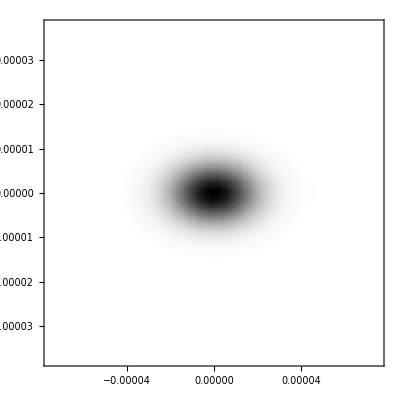

```mathematica
a=75*10^-6/2;
b=5*10^-6;
b=a/2;
DensityPlot[-Abs[U0]^2,{x2,-2a,2a},{y2,-2b,2b},PlotPoints->150,PlotRange->All,ColorFunction->GrayLevel]
```

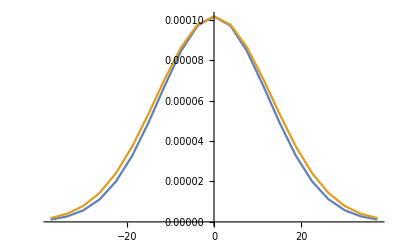

```mathematica
z=Subdivide[f-a,f+a,20];
uz=Abs[1/Sqrt[I λ z]*Integrate[U*Exp[I k/2(x^2+y^2)*(1/z-1/f)],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]]^2;

xl = Subdivide[-a,a,20];
ListPlot[{Transpose[{xl*10^6,uz}],Transpose[{xl*10^6,Abs[U0]^2/.y2->0/.x2->xl}]},Joined->True]
```

```mathematica
c = 299792458; (*m/s, Speed of Light in Vacuum*)
ℏ = 1.054571628*10^-34; (*J/s, Planck's constant*)
ϵ0 = 8.854187817*10^-12; (*F/m, Permittivity of Free Space*)
a0 = .529177*10^-10; (* Bohr radius, m *)
kB = 1.38*10^-23;
λ689 = 689*10^-9; (*m, in vacuum*)
λ698 = 698*10^-9; (*m, in vacuum*)
λ707 = 707*10^-9; (* m, in vacuum *)
λ813 = 813.4*10^-9; (*m, in vacuum*)
γ3p1 = 2π(7.5*10^3); (*rad/s, atom linewidth FWHM*)
γ3p0 = 2π(.001); (*rad/s, atom linewidth FWHM*)
γ461 = 32*10^6*2π;(*rad/s, atom linewidth FWHM*)
γ707  = 10*10^6*2π; (*NOT ACTUAL, USE FOR NOW*)
Isat461 = 42*10^-3*10^4; (* W/m^2*)
m = 87*1.66*10^-27; (* Sr 87, kg *)
α = 282*4π ϵ0 a0^3; (* dipole polarizability of ground, 3p0 at 813nm, from Boyd thesis *)
ωr = 4.7*1000*2π; (* recoil frequency clock trans ??? *)
```

```mathematica
λp = λ813/(2 Sin[θ/2]); 
Pbeam = .4; (* Incident power per beam *)
Pmax = 2Pbeam/(Pi wx0 wy0);
Ulattice = (α 4 Pbeam)/(ϵ0 c π wx0*wy0);
TrapDepthuK = 10^6 Ulattice/kB
TrapDepthHz = 1/(2π)Ulattice/ℏ;
ωtrap = 2π 1/λp √((2*Ulattice)/m);
```

33.6014

```mathematica
TrapDepthuK/100*kB*10^-6
```

4.637×10^-30

```mathematica
kl=2Pi/10^-6;
(TrapDepthuK*kB*10^-6)
(ℏ^2 kl^2/(2m))/(2Pi ℏ)
```

4.637×10^-28

2294.03

```mathematica
ℏ^2 /(2m)
```

```mathematica
TrapDepthHz
```

699812.

```mathematica
ωtrap/(2000Pi)
```

34.2149

```mathematica
ℏ 2Pi/(λp)^2/(2m)
```

1622.38

```mathematica
50 %
```

```mathematica
81119.19716881748
```

```mathematica
{TrapDepthHz,TrapDepthuK}/100
```

{74448.,3.57462}

```mathematica
J=300;
Sqrt[-wx0^2 Log[1-J/TrapDepthHz]/2]/(λ/2)
```

2.61917

```mathematica
2r/λ/.Solve[1-Exp[-2 r^2/(wx0)^2]==J/(TrapDepthHz/10)&&r>0,r][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

8.29007

```mathematica
J/TrapDepthHz
```

0.000402966

```mathematica
%/(λ/2)
```

364.751

```mathematica
λ//N
```

8.13×10^-7

```mathematica
TrapDepthHz
```

744480.

```mathematica
wx0//N
```

0.000075

```mathematica
(1.113*10^-16)/(6.748*10^24)
```

1.64938×10^-41

```mathematica
1.6487772754*10^-41
```

```mathematica
1/(ϵ0*c)
```

376.73

```mathematica
4π ϵ0 a0^3
```

1.64878×10^-41

```mathematica
Solve[λ F/(2*2*10^-2)==10^-5,F]//N
```

{{F→0.492005}}

```mathematica
d
```

3/100 Tan[20 °]

```mathematica
f=.3;
w0=100*10^-6;
λ f/w0
```

0.002439

```mathematica
d=10^-3;
NA = 0.12;
Sqrt[(d/NA)^2-d^2]
```

0.00827312

```mathematica
d^2/(3λ)//N
```

0.410004

```mathematica
1/(wy*wx)
```

7.97977×10^6

```mathematica
d//N
```

0.0109191

0.03

```mathematica
Sin[45Degree]
```

1/(√2)

28.1255

```mathematica
n=1.5;
θ2=ArcSin[1/Sqrt[2]/n];
d(1+Tan[Pi/4+θ2])
```

0.0469157

```mathematica
wx
wy
```

0.000207029

0.000605312

```mathematica
Solve[1/(3w^2)==10/10^-4,w]//N
```

{{w→-0.00182574},{w→0.00182574}}

```mathematica
Sin[0.01]*10^0
```

0.00999983

```mathematica
wy0//N
```

0.0000256515

```mathematica
λ/(2.5*10^-3)/Degree
```

0.0186326

```mathematica
2*Sqrt[2.]
```

2.82843

```mathematica
wx
wy
```

0.000207029

0.000605312